```mathematica
Es=Flatten[Import["/home/cjohns10/research/4BodySVD/eSpacings-150x60x60x200x100-m12.dat"]];eTrim = Select[Es,#>0.0000001&];
Length[Es]
Length[eTrim]
```

113

113

```mathematica
bins=Table[x,{x,0,5,0.2}];
```

```mathematica
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

```mathematica
EspaceBin=BinCounts[eTrim,{bins}];
```

```mathematica
NormBrodyBinCs=Table[EspaceBin[[i]]/Total[EspaceBin]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
```

```mathematica
Remove[al,p]
```

```mathematica
alpha[q_]:=(Gamma[(q+2)/(q+1)])^(q+1)
```

```mathematica
p[q_,s_]:=alpha[q]*(q+1)*s^(q)*E^(-alpha[q]*s^(q+1))
```

```mathematica
brodyPdist = Table[{bFit[[i]],NormBrodyBinCs[[i]]},{i,1,Length[bFit]}]
```

{{0.1,0.265487},{0.3,0.619469},{0.5,0.752212},{0.7,0.530973},{0.9,0.707965},{1.1,0.442478},{1.3,0.486726},{1.5,0.442478},{1.7,0.176991},{1.9,0.176991},{2.1,0.132743},{2.3,0.0442478},{2.5,0.176991},{2.7,0.},{2.9,0.0442478},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

```mathematica
p1=ListPlot[brodyPdist,InterpolationOrder->0,Joined->True,PlotRange->All];
```

```mathematica
pars = FindFit[brodyPdist,{p[q,s],q>0,q<1},{q},s]
```

{q→0.610636}

```mathematica
p2=Plot[p[q/.{q->0.1},s],{s,0,5},PlotRange->All];
```

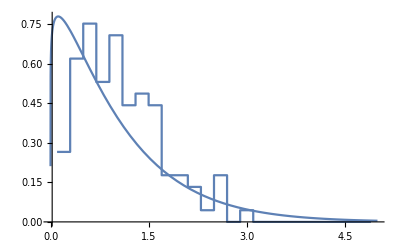

```mathematica
Show[p1,p2,PlotRange->All]
```